# Rendering of the double-triangle contribution to e^+e^-→γ^*→d d̄

## Resources

```mathematica
RustBindingsPath="/Users/valentin/Documents/MG5/3.0.2.py3/PLUGIN/alphaloop/Mathematica";
AlphaLoopPath="/Users/valentin/Documents/MG5/3.0.2.py3/PLUGIN/alphaloop";
```

```mathematica
(*Get[RustBindingsPath<>"/"<>"RustFromMathematica.m"]*)
Get[RustBindingsPath<>"/"<>"RustFromMathematicaV2.m"]
```

Package for accessing alphaLoop implementation in Rust.
This V2 version uses the faster approach of StartExternalSession[Python] to talk to alphaLoop.

Variables you may want to overwrite are:

RFM$LTDFolder = <Path>;
RFM$PythonInterpreter = <Path>;
RFM$CUBAPath = <Path>;
RFM$SCSPath=<Path>;
RFM$ECOSPath=<Path>;

The function: 
RFM$GetLTDHook[name_,OptionsPattern[
{
RunMode->'LTD',
HyperparametersPath->'LTD/hyperparameters.yaml',
TopologiesPath->'LTD/topologies.yaml',
AmplitudesPath->'LTD/anplitudes.yaml',
DEBUG->False
}

Allows you to generate a hook, which will automatically be placed in the list:

RFM$AllHooksStarted

Then you can test that one hook is active with:

RFM$CheckHookStatus[hook_]

And use them to access information from Rust with the following three API entry points (for now):

RFM$GetLTDDeformation[hook_, RealMomenta_,OptionsPattern[DEBUG->False]]
RFM$GetCrossSectionDeformation[hook_, CutID_,RealMomenta_,OptionsPattern[DEBUG->False]]
RFM$GetRescaling[hook_, CutID_,RealMomenta_,OptionsPattern[DEBUG->False]]
RFM$Parameterize[hook_,LoopIndex_,ECM_,Xs_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$InvParameterize[hook_,LoopIndex_,ECM_,Momentum_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$Evaluate[hook_,Momenta_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$EvaluateCut[hook_,CutID_,scalingFactor_, scalingFactorJacobian_,Momenta_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$EvaluateIntegrand[hook_,Xs_,OptionsPattern[{DEBUG->False,f128->False}]]

Specify the running process path. It can be generated with the following command:

./bin/mg5_aMC --mode=alphaloop PLUGIN/alphaloop/examples/epem_a_ddx_paper_rendering_DT.aL

but making sure you have Q^μ=(2,0,0,0)

```mathematica
ProcessPath="/Users/valentin/Documents/MG5/3.0.2.py3/epem_a_ddx_paper_rendering_DT";
```

Specify the LTD folder to the hook package:

```mathematica
RFM$LTDFolder=AlphaLoopPath;
```

Make sure a stat folder exists in the local directory:

```mathematica
If[Not[DirectoryQ[NotebookDirectory[]<>"/stats"]],CreateDirectory[NotebookDirectory[]<>"stats"]];
```

Generic expression of ellipsoids, we will consider the triangle loop graph in k-space (i.e. to the left of the cutkosky cut, so cut_ID=2), with the following momentum routing:

-Graphics-

```mathematica
Ellipsoids[k_,p_,m_,p0_,N_]:=Flatten[Table[{Sqrt[Total[(k+p[[i]])^2]+ m[[i]]]+Sqrt[Total[(k+p[[j]])^2]+ m[[j]]]+p0[[j]]-p0[[i]]<0, Sqrt[Total[(k+p[[i]])^2]+ m[[i]]]+Sqrt[Total[(k+p[[j]])^2]+ m[[j]]]-p0[[j]]+p0[[i]]<0},{i, 1,N},{j,i+1,N}]]
```

Clean monofont print with Sleep safety

```mathematica
MyPrint[msg_]:=Block[{},Pause[0.1];Print[Style[msg,FontFamily->"Monaco"]]]
```

Get the hook to various deformation functional choices

First clean up all existing ones

```mathematica
GetHook[processPath_,yamlPath_,OptionsPattern[{hyperparameters->"inclusive_no_MC_no_deformation.yaml",DEBUG->False}]]:=Block[{},
RFM$GetLTDHook[yamlPath,
RunMode->"cross_section",
HyperparametersPath->NotebookDirectory[]<>"/hyperparameters/"<>OptionValue[hyperparameters],
DEBUG->OptionValue[DEBUG],
MGNumeratorPath->processPath
]
]
```

```mathematica
RefreshHooks[]:=Module[{},
RFM$KillAllHooks[];
HookInclusiveNoMCNoDeformation=GetHook[ProcessPath,ProcessPath<>"/FORM/Rust_inputs/P0L1R2.yaml",
hyperparameters->"inclusive_no_MC_no_deformation.yaml"];
HookInclusiveMCNoDeformation=GetHook[ProcessPath,ProcessPath<>"/FORM/Rust_inputs/P0L1R2.yaml",
hyperparameters->"inclusive_MC_no_deformation.yaml"];
HookInclusiveNoMCDeformation=GetHook[ProcessPath,ProcessPath<>"/FORM/Rust_inputs/P0L1R2.yaml",
hyperparameters->"inclusive_no_MC_deformation.yaml"];
HookInclusiveMCDeformation=GetHook[ProcessPath,ProcessPath<>"/FORM/Rust_inputs/P0L1R2.yaml",
hyperparameters->"inclusive_MC_deformation.yaml"];
HookSemiInclusiveNoMCDeformation=GetHook[ProcessPath,ProcessPath<>"/FORM/Rust_inputs/P0L1R2.yaml",
hyperparameters->"semi_inclusive_no_MC_deformation.yaml"];
HookSemiInclusiveMCDeformation=GetHook[ProcessPath,ProcessPath<>"/FORM/Rust_inputs/P0L1R2.yaml",
hyperparameters->"semi_inclusive_MC_deformation.yaml"];
HookSemiInclusiveNoMCNoDeformation=GetHook[ProcessPath,ProcessPath<>"/FORM/Rust_inputs/P0L1R2.yaml",
hyperparameters->"semi_inclusive_no_MC_no_deformation.yaml"];
HookSemiInclusiveMCNoDeformation=GetHook[ProcessPath,ProcessPath<>"/FORM/Rust_inputs/P0L1R2.yaml",
hyperparameters->"semi_inclusive_MC_no_deformation.yaml"];
{
RFM$CheckHookStatus[HookInclusiveNoMCNoDeformation],
RFM$CheckHookStatus[HookInclusiveMCNoDeformation],
RFM$CheckHookStatus[HookInclusiveNoMCDeformation],
RFM$CheckHookStatus[HookInclusiveMCDeformation],
RFM$CheckHookStatus[HookSemiInclusiveNoMCDeformation],
RFM$CheckHookStatus[HookSemiInclusiveMCDeformation],
RFM$CheckHookStatus[HookSemiInclusiveNoMCNoDeformation],
RFM$CheckHookStatus[HookSemiInclusiveMCNoDeformation]
}
]
```

```mathematica
RefreshHooks[]
```

{True,True,True,True,True,True,True,True}

Set below the desired point density for the heat maps

```mathematica
HeatMapDensity=10;
```

And for the vector fields:

```mathematica
VectorFieldDensity=20;
```

Useful 3D euclidean norm

```mathematica
VDot[k_]:=k⟦1⟧^2+k⟦2⟧^2+k⟦3⟧^2
```

## Ellipsoids and kinematics definition and access functions

```mathematica
Ellipsoids[k_,p_,m_,p0_,N_,OptionsPattern[{Contour->False}]]:=Flatten[Table[
If[OptionValue[Contour],
{Sqrt[Total[(k+p[[i]])^2]+ m[[i]]]+Sqrt[Total[(k+p[[j]])^2]+ m[[j]]]+p0[[j]]-p0[[i]]==0, Sqrt[Total[(k+p[[i]])^2]+ m[[i]]]+Sqrt[Total[(k+p[[j]])^2]+ m[[j]]]-p0[[j]]+p0[[i]]==0},
{Sqrt[Total[(k+p[[i]])^2]+ m[[i]]]+Sqrt[Total[(k+p[[j]])^2]+ m[[j]]]+p0[[j]]-p0[[i]]<0, Sqrt[Total[(k+p[[i]])^2]+ m[[i]]]+Sqrt[Total[(k+p[[j]])^2]+ m[[j]]]-p0[[j]]+p0[[i]]<0}
],{i, 1,N},{j,i+1,N}]]
```

```mathematica
TriangleP1={0,0,0};
TriangleP10=2.0;
TriangleP2={N[1/Sqrt[2],16],N[1/Sqrt[2],16],0};
TriangleP20=Sqrt[VDot[TriangleP2]];
```

Apply rescaling

```mathematica
GetRescaling[l_]:=Block[{RescalingSolutions},
RescalingSolutions=RFM$GetRescaling[HookInclusiveNoMCNoDeformation,1,{{0,0,0},l}];
If[RescalingSolutions["tSolutions"]⟦1⟧>0,
{RescalingSolutions["tSolutions"]⟦1⟧,RescalingSolutions["tJacobians"]⟦1⟧},
{RescalingSolutions["tSolutions"]⟦2⟧,RescalingSolutions["tJacobians"]⟦2⟧}
]
]
```

```mathematica
RescalingFactor=GetRescaling[TriangleP2]⟦1⟧;
RescalingJacobian=GetRescaling[TriangleP2]⟦2⟧;
TriangleP2*= RescalingFactor;
TriangleP20*=RescalingFactor;
SoftPoint=TriangleP2*RescalingFactor;
```

Now that the kinematics is set, generate all ellipsoids

```mathematica
AllTriangleEllipsoids=Ellipsoids[{kx,ky,0},{TriangleP1,TriangleP1+TriangleP2,0},{0,0,0},{TriangleP10,TriangleP10+TriangleP20,0},3,Contour->False];
AllTriangleEllipsoidsContour=Ellipsoids[{kx,ky,0},{TriangleP1,TriangleP1+TriangleP2,0},{0,0,0},{TriangleP10,TriangleP10+TriangleP20,0},3,Contour->True];
```

And define functions accessing the deformation for the particular case of interest

```mathematica
GetDeformationVector[kx_?NumberQ,ky_?NumberQ,kz_?NumberQ,OptionsPattern[{hook->HookInclusiveNoMCDeformation,cutID->1}]]:=Block[{DeformedMomenta},
DeformedMomenta=RFM$GetCrossSectionDeformation[OptionValue[hook],OptionValue[cutID],{{kx,ky,kz},TriangleP2/RescalingFactor},DEBUG->False];
Im[-DeformedMomenta["DeformedMomenta"]]
]
```

```mathematica
GetDeformationVectorXY[kx_?NumericQ,ky_?NumberQ]:=Block[
{Kappas},
Kappas=GetDeformationVector[kx/RescalingFactor,ky/RescalingFactor,TriangleP2⟦3⟧/RescalingFactor];
{Kappas⟦1⟧⟦2⟧,Kappas⟦1⟧⟦3⟧}
]
```

```mathematica
EvaluateCutXY[hook_,kx_?NumericQ,ky_?NumberQ,OptionsPattern[{DEBUG->False,CUTID->1}]]:=Block[
{},
If[OptionValue[DEBUG],Print["kx="<>ToString[kx,InputForm]<>" "<>"ky="<>ToString[ky,InputForm]];];
RFM$EvaluateCut[hook,OptionValue[CUTID],RescalingFactor,RescalingJacobian,{{kx/RescalingFactor,ky/RescalingFactor,TriangleP2⟦3⟧/RescalingFactor},TriangleP2/RescalingFactor},DEBUG->False,f128->False]
]
```

```mathematica
EvaluateFullXY[hook_,kx_?NumericQ,ky_?NumberQ,OptionsPattern[DEBUG->False]]:=Block[
{invParametrizeK,invParametrizeL},
If[OptionValue[DEBUG],Print["kx="<>ToString[kx,InputForm]<>" "<>"ky="<>ToString[ky,InputForm]];];
invParametrizeK=RFM$InvParameterize[hook,0,2,{kx/RescalingFactor,ky/RescalingFactor,TriangleP2⟦3⟧/RescalingFactor},DEBUG->OptionValue[DEBUG]]["Xs"];
If[OptionValue[DEBUG],Print["Xs for loop momentum k = "<>StringJoin[Table[ToString[x,InputForm],{x,invParametrizeK}]]]];
invParametrizeL=RFM$InvParameterize[hook,1,2,TriangleP2/RescalingFactor,DEBUG->OptionValue[DEBUG]]["Xs"];
If[OptionValue[DEBUG],Print["Xs for loop momentum l = "<>StringJoin[Table[ToString[x,InputForm],{x,invParametrizeL}]]]];
RFM$EvaluateIntegrand[hook,Join[invParametrizeK,invParametrizeL],DEBUG->OptionValue[DEBUG]]
]
```

## DT integrand Rendering

### Commons

Common resources beloow

```mathematica
Pt[mom_]:=Sqrt[mom⟦1⟧^2+mom⟦2⟧^2];
```

```mathematica
ScannedMomentum[ky_]:={0,ky,N[1/Sqrt[2],16]};
```

```mathematica
CutLowerBounds=Sort[Table[ky/.sol,{sol,Solve[Pt[ScannedMomentum[ky]] 1/Sqrt[VDot[ScannedMomentum[ky]]]==0.4,ky]}]]
```

{-0.308607,0.308607}

```mathematica
CutUpperBounds=Sort[Table[ky/.sol,{sol,Solve[Pt[ScannedMomentum[ky]] 1/Sqrt[VDot[ScannedMomentum[ky]]]==0.8,ky]}]]
```

{-0.942809,0.942809}

```mathematica
MakeALabeledPoint[location_,label_]:=Block[{},
{Graphics[{PointSize->0.01,Red, Point[location]}],Graphics[{Red,FontSize->15,Text[label,location+{0.1,-0.01}]}]}
]
```

Aliasing cut IDs

```mathematica
CutIDRA=0;
CutIDRB=3;
CutIDLxB=2;
CutIDBxL=1;
```

### Now vary the y component of K the z component of L

Now let’s highlight in this fashion E-surface cancellation, and their non-locality in the presence of a cut, which we shall do by plotting things for cut2 and cut3 (corresponding to the triangle on the right of the Cutkosky Cut, respectively left of it).

For this we will, consider 2D plots where we vary k_y and l_y in k=(0,ky,1/Sqrt[2]) and l=(0,ly,1/Sqrt[2]).

```mathematica
ScannedMomentumK[ky_]:={0,ky,N[1/Sqrt[2],16]};
ScannedMomentumL[lz_]:={0,N[1/Sqrt[2],16],lz};
```

```mathematica
CutBoundsInL=Sort[Table[lz/.sol,{sol,Solve[Pt[ScannedMomentumL[lz]]/Sqrt[VDot[ScannedMomentumL[lz]]]==0.8,lz]}]]
```

{-0.53033,0.53033}

And define functions accessing the deformation for the particular case of interest

```mathematica
EvaluateCutForKLScanYZ[hook_,kComp_?NumericQ,lComp_?NumberQ,
OptionsPattern[{DEBUG->False,cutID->CutIDLxB, RotatedBasis->False,IncludeJacobian->False,ECM->2}]]:=Block[
{kvec,lvec, rescaling,rescalingSelected,jacobian=1.,lvecTMP,kvecTMP},
kvec=ScannedMomentumK[kComp];
lvec=ScannedMomentumL[lComp];
rescaling=RFM$GetRescaling[hook,OptionValue[cutID],{kvec,lvec}];
rescalingSelected=If[rescaling["tSolutions"]⟦1⟧>0,
{rescaling["tSolutions"]⟦1⟧,rescaling["tJacobians"]⟦1⟧},
{rescaling["tSolutions"]⟦2⟧,rescaling["tJacobians"]⟦2⟧}
];
If[OptionValue[IncludeJacobian],
kvecTMP=kvec;
If[OptionValue[RotatedBasis],
lvecTMP=lvec-kvec;,
lvecTMP=lvec;
];
jacobian=(RFM$InvParameterize[hook,0,OptionValue[ECM]^2,kvecTMP,DEBUG->OptionValue[DEBUG],f128->True]["Jacobian"]*
RFM$InvParameterize[hook,1,OptionValue[ECM]^2,lvecTMP,DEBUG->OptionValue[DEBUG],f128->True]["Jacobian"])
]; 
If[And[OptionValue[DEBUG],OptionValue[IncludeJacobian]],MyPrint["Jacobian="<>ToString[jacobian,InputForm]]];
If[OptionValue[DEBUG],MyPrint["Rescaling="<>ToString[rescalingSelected⟦1⟧,InputForm]]];
(* We could evaluate the cuts ourselves too *)
If[OptionValue[DEBUG],MyPrint["Pt(k)="<>ToString[Pt[kvec],InputForm]]];
If[OptionValue[DEBUG],MyPrint["Pt(l)="<>ToString[Pt[lvec],InputForm]]];
(*If[OptionValue[cutID]==1&&Not[0.4<Pt[kvec]<0.8],Return[0.]];*)
(*If[OptionValue[cutID]==2&&Not[0.4<Pt[lvec]<0.8],Return[0.]];*)
(1.0/jacobian)*RFM$EvaluateCut[hook,OptionValue[cutID],rescalingSelected⟦1⟧,rescalingSelected⟦2⟧,{kvec,lvec},DEBUG->OptionValue[DEBUG],f128->True]
]
```

```mathematica
EvaluateFullForKLScanYZ[hook_,kComp_?NumericQ,lComp_?NumberQ,OptionsPattern[{DEBUG->False,ECM->2, RotatedBasis->False,IncludeJacobian->False}]]:=Block[
{kvec,lvec,invParametrizeK,JacobianK,invParametrizeL,JacobianL,invP,res},
kvec=ScannedMomentumK[kComp];
lvec=ScannedMomentumL[lComp];
If[OptionValue[RotatedBasis],
lvec=lvec-kvec;
];
invP=RFM$InvParameterize[hook,0,OptionValue[ECM]^2,kvec,DEBUG->OptionValue[DEBUG]];
invParametrizeK=invP["Xs"];
JacobianK=invP["Jacobian"];
If[OptionValue[DEBUG],Print["Xs for loop momentum k = "<>StringJoin[Table[ToString[x,InputForm],{x,invParametrizeK}]]]];
invP=RFM$InvParameterize[hook,1,OptionValue[ECM]^2,lvec,DEBUG->OptionValue[DEBUG]];
invParametrizeL=invP["Xs"];
JacobianL=invP["Jacobian"];
If[OptionValue[DEBUG],Print["Xs for loop momentum l = "<>StringJoin[Table[ToString[x,InputForm],{x,invParametrizeL}]]]];
res=RFM$EvaluateIntegrand[hook,Join[invParametrizeK,invParametrizeL],DEBUG->OptionValue[DEBUG]];
If[Not[OptionValue[IncludeJacobian]],res JacobianK JacobianL,res]
]
```

Testing the above functions below

```mathematica
(* RefreshHooks[]*)
```

```mathematica
EvaluateCutForKLScanYZ[HookInclusiveNoMCNoDeformation,N[1/Sqrt[2]],N[1/Sqrt[2]]+0.002,cutID->CutIDBxL,DEBUG->True,RotatedBasis->False,IncludeJacobian->True]
```

Jacobian=0.00031154244681764646

Rescaling=0.9985867878453525

Pt(k)=0.7071067811865475

Pt(l)=0.70710678118654752440084436210484070353`16.

-5.15567×10^12+0.0000903175 ⅈ

```mathematica
EvaluateFullForKLScanYZ[HookInclusiveNoMCNoDeformation,N[1/Sqrt[2]],N[1/Sqrt[2]]+0.001,ECM->CutIDBxL,DEBUG->True,IncludeJacobian->True]
```

Xs for loop momentum k = 0.50.250.8535533905932737

Xs for loop momentum l = 0.50017677662906780.250.8538031256156755

1.73424×10^7+0.00017255 ⅈ

Generating the common background lines

```mathematica
AllThresholdLinesForKLScanInLxBYZ=Graphics[
{
{Purple,Thick,Line[{{-1.3,-1.3},{1.3,1.3}}]},
{Purple,Thick,Line[{{-1.3,1.3},{1.3,-1.3}}]},
{Blue,Thick,Line[{{CutUpperBounds⟦1⟧,-1.3},{CutUpperBounds⟦1⟧,1.3}}]},
{Blue,Thick,Line[{{CutLowerBounds⟦1⟧,-1.3},{CutLowerBounds⟦1⟧,1.3}}]},
{Blue,Thick,Line[{{CutLowerBounds⟦2⟧,-1.3},{CutLowerBounds⟦2⟧,1.3}}]},
{Blue,Thick,Line[{{CutUpperBounds⟦2⟧,-1.3},{CutUpperBounds⟦2⟧,1.3}}]}
}];
```

```mathematica
AllThresholdLinesForKLScanInBxLYZ=Graphics[
{
{Purple,Thick,Line[{{-1.3,-1.3},{1.3,1.3}}]},
{Purple,Thick,Line[{{-1.3,1.3},{1.3,-1.3}}]},
{Blue,Thick,Line[{{-1.3,CutBoundsInL⟦1⟧},{1.3,CutBoundsInL⟦1⟧}}]},
{Blue,Thick,Line[{{-1.3,CutBoundsInL⟦2⟧},{1.3,CutBoundsInL⟦2⟧}}]}
}];
```

```mathematica
AllThresholdLinesForKLScanInSumYZ=Graphics[
{
{Purple,Thick,Line[{{-1.3,-1.3},{1.3,1.3}}]},
{Purple,Thick,Line[{{-1.3,1.3},{1.3,-1.3}}]},
{Blue,Thick,Line[{{CutUpperBounds⟦1⟧,-1.3},{CutUpperBounds⟦1⟧,1.3}}]},
{Blue,Thick,Line[{{CutLowerBounds⟦1⟧,-1.3},{CutLowerBounds⟦1⟧,1.3}}]},
{Blue,Thick,Line[{{CutLowerBounds⟦2⟧,-1.3},{CutLowerBounds⟦2⟧,1.3}}]},
{Blue,Thick,Line[{{CutUpperBounds⟦2⟧,-1.3},{CutUpperBounds⟦2⟧,1.3}}]},
{Blue,Thick,Line[{{-1.3,CutBoundsInL⟦1⟧},{1.3,CutBoundsInL⟦1⟧}}]},
{Blue,Thick,Line[{{-1.3,CutBoundsInL⟦2⟧},{1.3,CutBoundsInL⟦2⟧}}]}
}];
```

### Density heat map, with No deformation

Now Study the no-deformation case!

```mathematica
RefreshHooks[]
```

{True,True,True,True,True,True,True,True}

```mathematica
DensityForThisSection=30;
PerformanceGoalForThisSection="Quality";
MaxRecursionForThisSection=4;
HookForThisSection=HookSemiInclusiveNoMCNoDeformation;
ImageSizeForThisSection=Large;
IncludeJacobianInThisSection=False;
kyRegulationThisSection=10^-5;
```

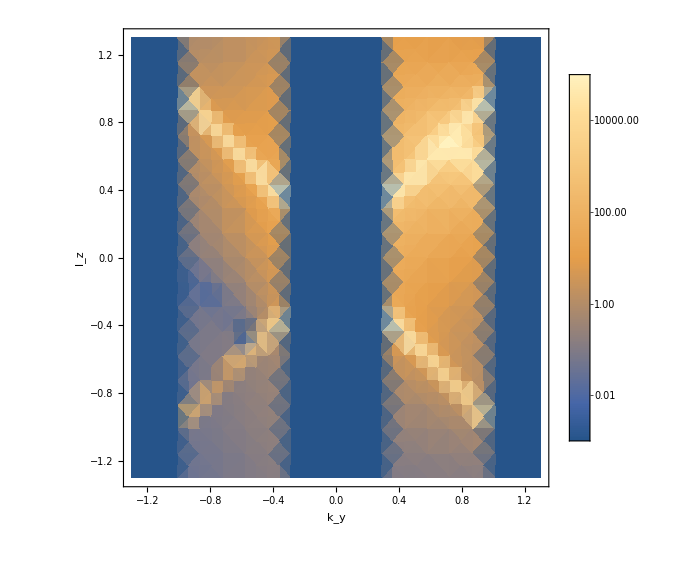

```mathematica
KLScanDensityPlotLxBReYZColouredNoDeformation=Block[
{},
DensityPlot[
Min[Max[Abs[Re[EvaluateCutForKLScanYZ[HookForThisSection,ky+kyRegulationThisSection,lz,cutID->CutIDLxB,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]]],1.0*^-3],1.0*^5],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotLegends->Automatic,
ScalingFunctions->"Log",
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->MaxRecursionForThisSection,PlotRange->All,
Frame->True,ImageSize->ImageSizeForThisSection,PerformanceGoal->PerformanceGoalForThisSection]
]
```

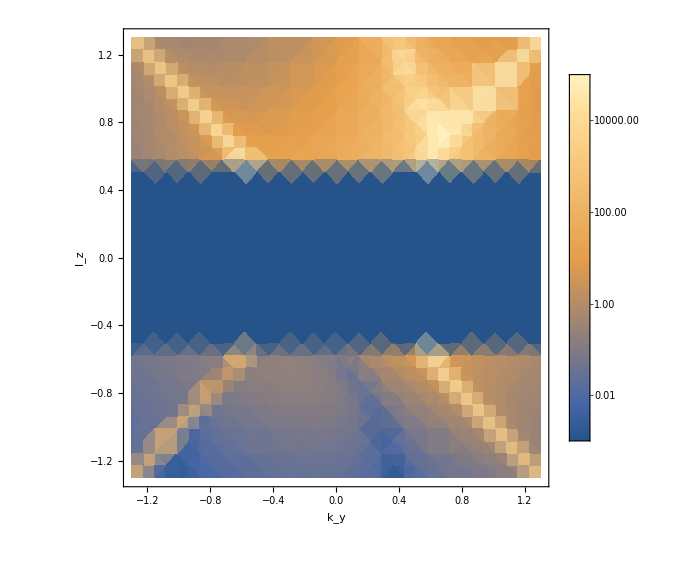

```mathematica
KLScanDensityPlotBxLReYZColouredNoDeformation=Block[
{},
DensityPlot[Min[Max[Abs[Re[EvaluateCutForKLScanYZ[HookForThisSection,ky+kyRegulationThisSection,lz,cutID->CutIDBxL,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]]],1.0*^-3],1*^5],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
ScalingFunctions->"Log",
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->MaxRecursionForThisSection,PlotRange->All,
Frame->True,
PlotLegends->True,
ImageSize->ImageSizeForThisSection,PerformanceGoal->PerformanceGoalForThisSection]
]
```

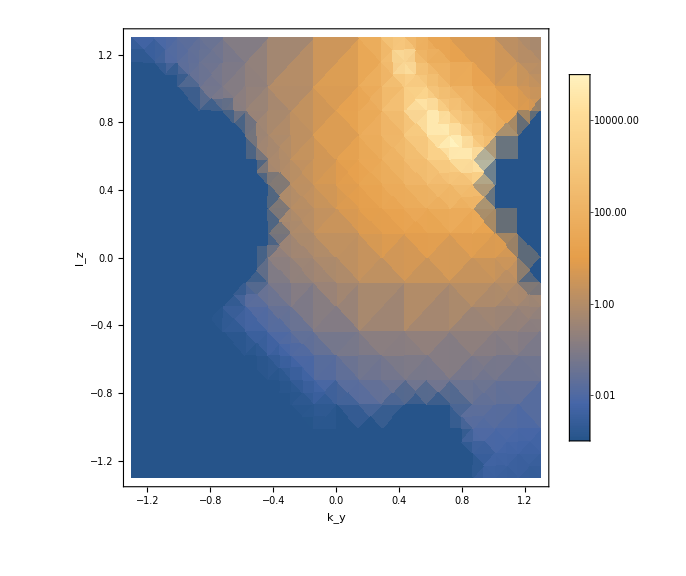

```mathematica
KLScanDensityPlotRealYZColouredNoDeformation=Block[
{},
DensityPlot[Min[Max[2Abs[Re[EvaluateCutForKLScanYZ[HookForThisSection,ky+kyRegulationThisSection,lz,cutID->CutIDRA,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]]],1.0*^-3],1*^5],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotLegends->Automatic,
ScalingFunctions->"Log",
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->MaxRecursionForThisSection,PlotRange->All,
Frame->True,
ImageSize->ImageSizeForThisSection,PerformanceGoal->PerformanceGoalForThisSection]
]
```

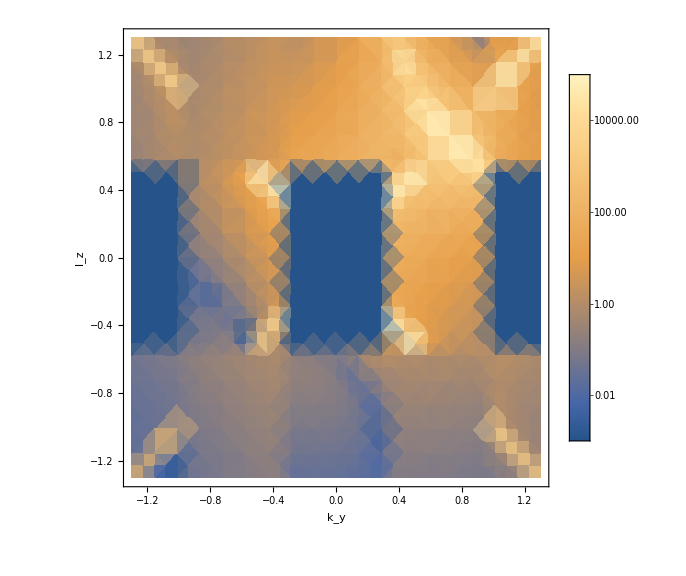

```mathematica
KLScanDensityPlotSumReYZColouredNoDeformation=Block[
{},
DensityPlot[Min[Max[Abs[Re[
EvaluateCutForKLScanYZ[HookForThisSection,ky+kyRegulationThisSection,lz,cutID->CutIDLxB,DEBUG->False,IncludeJacobian->False]+
EvaluateCutForKLScanYZ[HookForThisSection,ky+kyRegulationThisSection,lz,cutID->CutIDBxL,DEBUG->False,IncludeJacobian->False]]
],1.0*^-3],1.0*^5],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
ScalingFunctions->"Log",
PlotLegends->Automatic,
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->MaxRecursionForThisSection,PlotRange->All,
Frame->True,
PlotLegends->Automatic,ScalingFunctions->"Log",
ImageSize->ImageSizeForThisSection,PerformanceGoal->PerformanceGoalForThisSection]
]
```

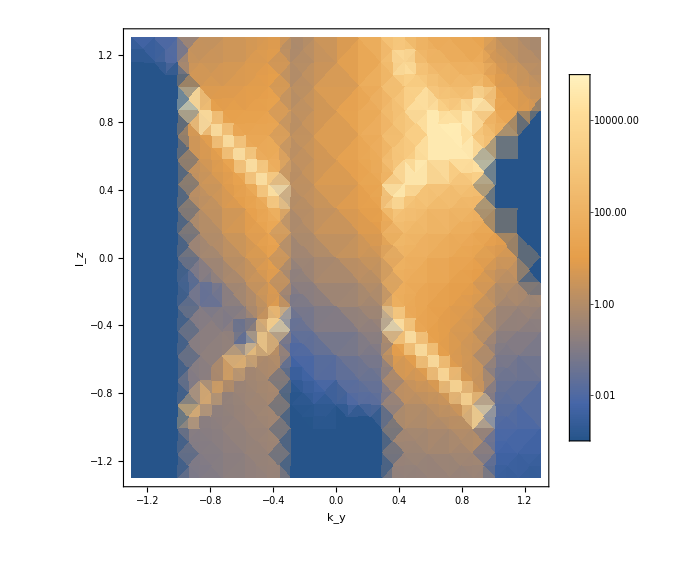

```mathematica
KLScanDensityPlotAllReYZColouredNoDeformation=Block[
{},
DensityPlot[Min[Max[Abs[Re[
EvaluateCutForKLScanYZ[HookForThisSection,ky+kyRegulationThisSection,lz,cutID->CutIDLxB,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]+
EvaluateCutForKLScanYZ[HookForThisSection,ky+kyRegulationThisSection,lz,cutID->CutIDLxB,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]+
2EvaluateCutForKLScanYZ[HookForThisSection,ky+kyRegulationThisSection,lz,cutID->CutIDRA,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]
]
],1.0*^-3],1.0*^5],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
ScalingFunctions->"Log",
PlotLegends->Automatic,
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->MaxRecursionForThisSection,PlotRange->All,
Frame->True,
ImageSize->ImageSizeForThisSection,PerformanceGoal->PerformanceGoalForThisSection]
]
```

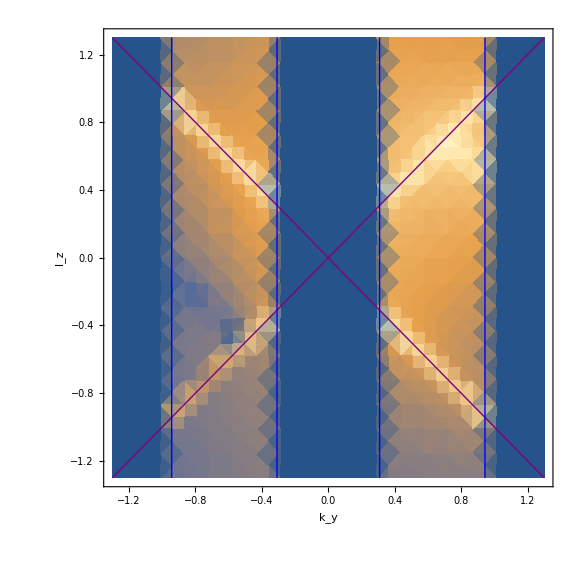
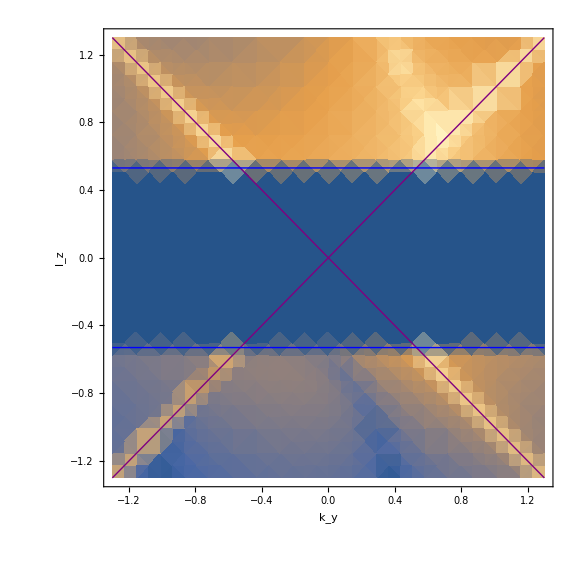
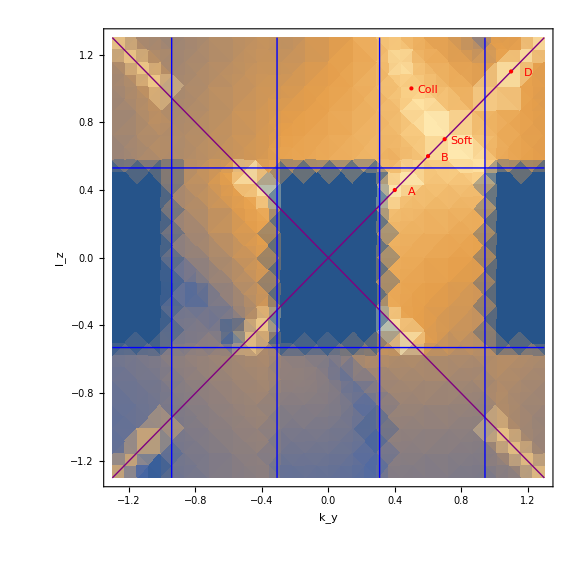
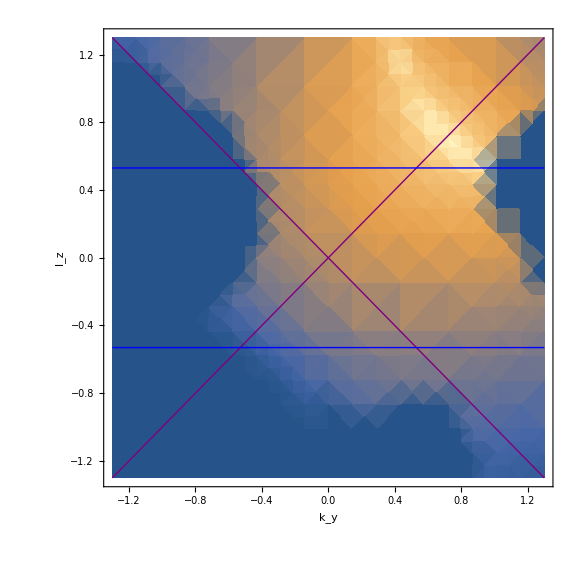
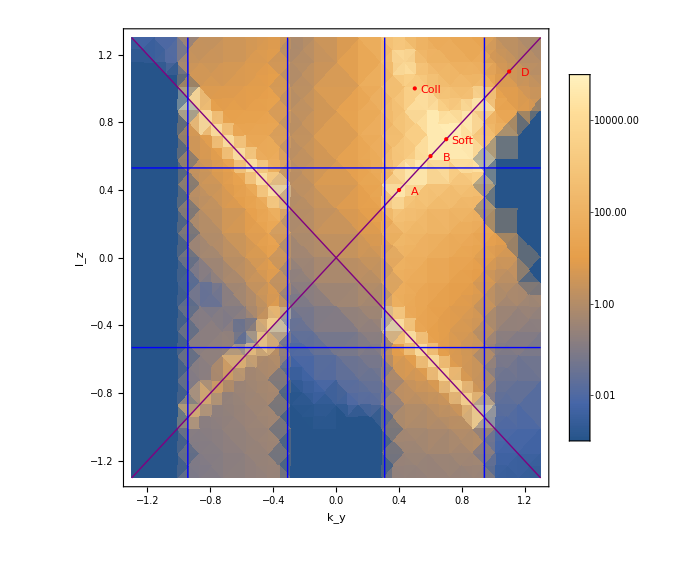
-Graphics-LxB( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) ) | -Graphics-BxL( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) ) | -Graphics-(LxB+BxL)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )
-Graphics-(RA+RB)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) ) | -Graphics-(LxB+BxL+RA+RB)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) ) |

```mathematica
Grid[{
{
Labeled[Show[KLScanDensityPlotLxBReYZColouredNoDeformation⟦1⟧,AllThresholdLinesForKLScanInLxBYZ,ImageSize->Large],"LxB( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )"],
Labeled[Show[KLScanDensityPlotBxLReYZColouredNoDeformation⟦1⟧,AllThresholdLinesForKLScanInBxLYZ,ImageSize->Large],"BxL( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )"],
Labeled[Show[{KLScanDensityPlotSumReYZColouredNoDeformation⟦1⟧,AllThresholdLinesForKLScanInSumYZ,
Sequence[MakeALabeledPoint[{0.4,0.4},"A"]],
Sequence[MakeALabeledPoint[{0.6,0.6},"B"]],
Sequence[MakeALabeledPoint[{0.7,0.7},"Soft"]],
Sequence[MakeALabeledPoint[{1.1,1.1},"D"]],
Sequence[MakeALabeledPoint[{0.5,1.0},"Coll"]]
},ImageSize->Large],"(LxB+BxL)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )"]},
{
Labeled[Show[KLScanDensityPlotRealYZColouredNoDeformation⟦1⟧,AllThresholdLinesForKLScanInBxLYZ,ImageSize->Large],"(RA+RB)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )"],
Labeled[Show[{KLScanDensityPlotAllReYZColouredNoDeformation,AllThresholdLinesForKLScanInSumYZ,
Sequence[MakeALabeledPoint[{0.4,0.4},"A"]],
Sequence[MakeALabeledPoint[{0.6,0.6},"B"]],
Sequence[MakeALabeledPoint[{0.7,0.7},"Soft"]],
Sequence[MakeALabeledPoint[{1.1,1.1},"D"]],
Sequence[MakeALabeledPoint[{0.5,1.0},"Coll"]]
},ImageSize->Large],"(LxB+BxL+RA+RB)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )"]
}
},ItemSize->{55,35}]
```

### Density heat map, with deformation

And now the same but with actual a full colour scale on the density plot

```mathematica
RefreshHooks[];
```

```mathematica
DensityForThisSection=30;
PerformanceGoalForThisSection="Quality";
MaxRecursionForThisSection=4;
ImageSizeForThisSection=Large;
IncludeJacobianInThisSection=False;
kyRegulationThisSection=10^-5;
```

```mathematica
HookForThisSection=HookSemiInclusiveNoMCDeformation;
```

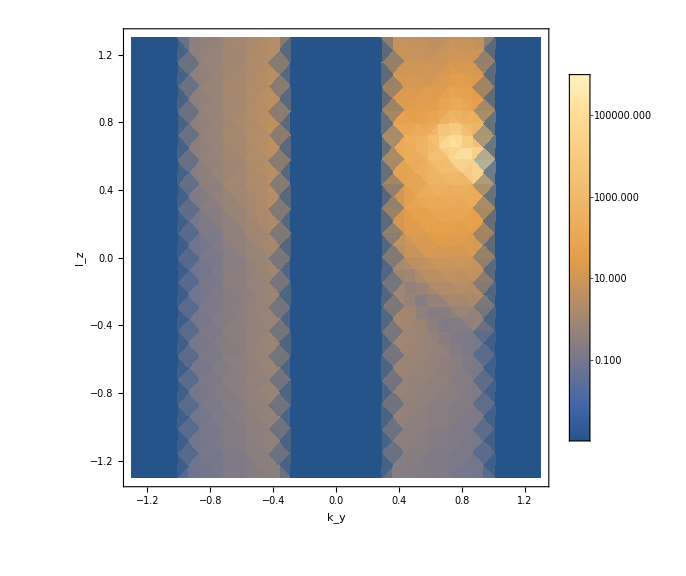

```mathematica
KLScanDensityPlotLxBReYZColoured=Block[
{},
DensityPlot[Min[Max[Abs[Re[EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,ky+kyRegulationThisSection,lz,cutID->CutIDLxB,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]]],1.0*^-3],10*^5],
{ky,-1.3,1.3},
{lz,-1.3,1.3},
PlotLegends->Automatic,ScalingFunctions->"Log",
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->MaxRecursionForThisSection,
Frame->True,
ImageSize->ImageSizeForThisSection,PerformanceGoal->PerformanceGoalForThisSection]
]
```

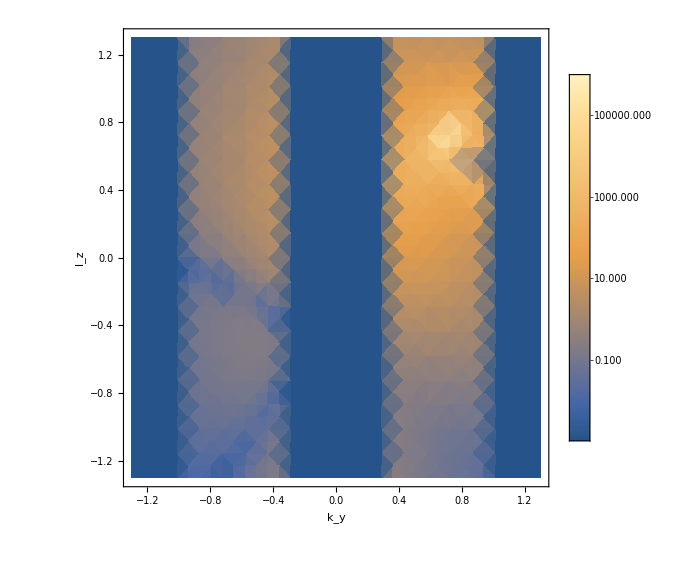

```mathematica
KLScanDensityPlotLxBImYZColoured=Block[
{},
DensityPlot[Min[Max[Abs[Im[EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,ky+kyRegulationThisSection,lz,cutID->CutIDLxB,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]]],1.0*^-3],10*^5],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotLegends->Automatic,ScalingFunctions->"Log",
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->MaxRecursionForThisSection,
Frame->True,
ImageSize->ImageSizeForThisSection,PerformanceGoal->PerformanceGoalForThisSection]
]
```

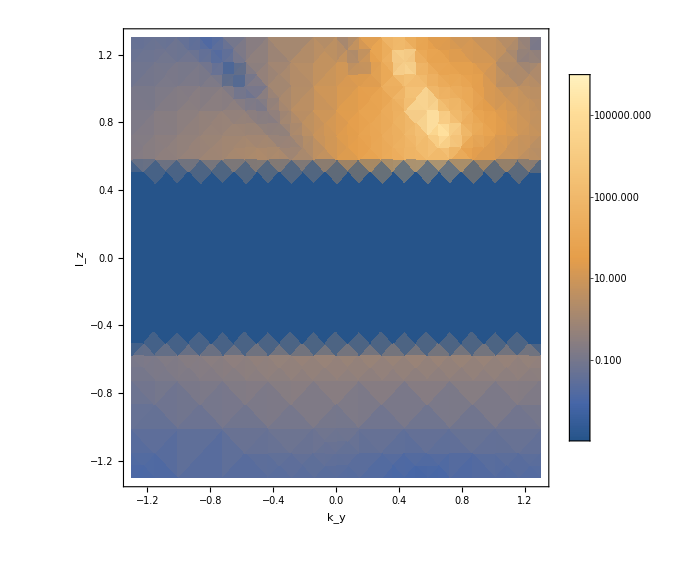

```mathematica
KLScanDensityPlotBxLReYZColoured=Block[
{},
DensityPlot[Min[Max[Abs[Re[EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,ky+kyRegulationThisSection,lz,cutID->CutIDBxL,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]]],1.0*^-3],10*^5],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotLegends->Automatic,ScalingFunctions->"Log",
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->MaxRecursionForThisSection,
Frame->True,
ImageSize->ImageSizeForThisSection,PerformanceGoal->PerformanceGoalForThisSection]
]
```

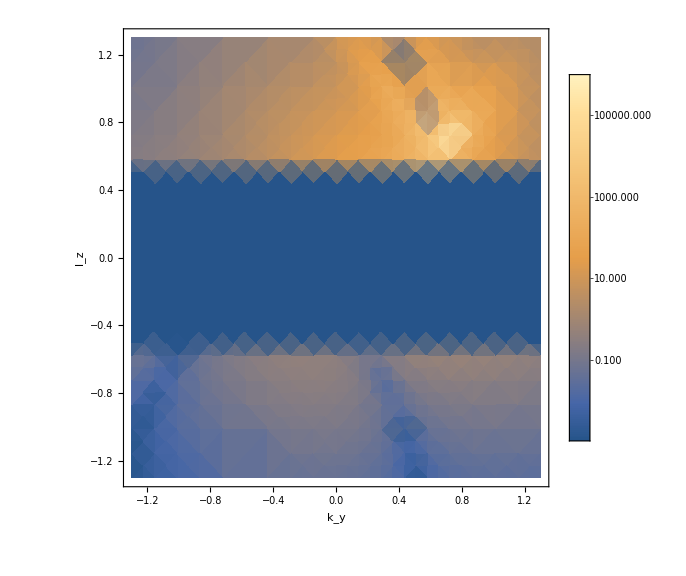

```mathematica
KLScanDensityPlotBxLImYZColoured=Block[
{},
DensityPlot[Min[Max[Abs[Im[EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,ky+kyRegulationThisSection,lz,cutID->CutIDBxL,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]]],1.0*^-3],10*^5],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotLegends->Automatic,ScalingFunctions->"Log",
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->MaxRecursionForThisSection,
Frame->True,
ImageSize->ImageSizeForThisSection,PerformanceGoal->PerformanceGoalForThisSection]
]
```

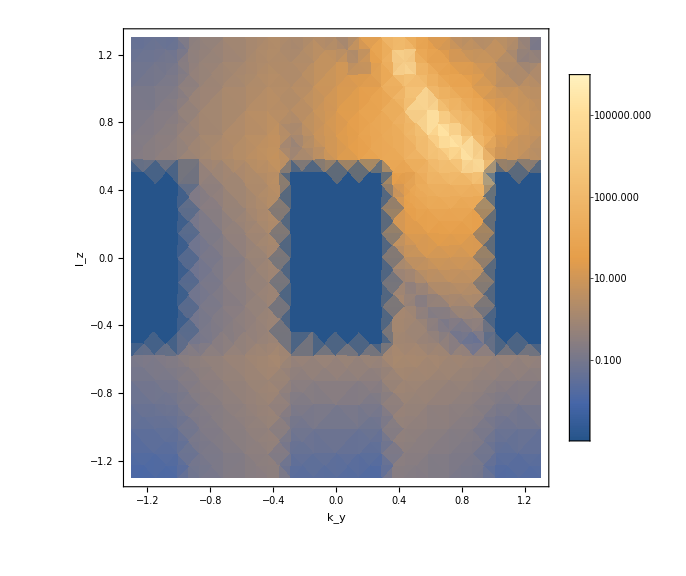

```mathematica
KLScanDensityPlotSumReYZColoured=Block[
{},
DensityPlot[Min[Max[Abs[Re[
EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,ky+kyRegulationThisSection,lz,cutID->CutIDLxB,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]+
EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,ky+kyRegulationThisSection,lz,cutID->CutIDBxL,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]]
],1.0*^-3],10*^5],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotLegends->Automatic,ScalingFunctions->"Log",
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->MaxRecursionForThisSection,
Frame->True,
ImageSize->ImageSizeForThisSection,PerformanceGoal->PerformanceGoalForThisSection]
]
```

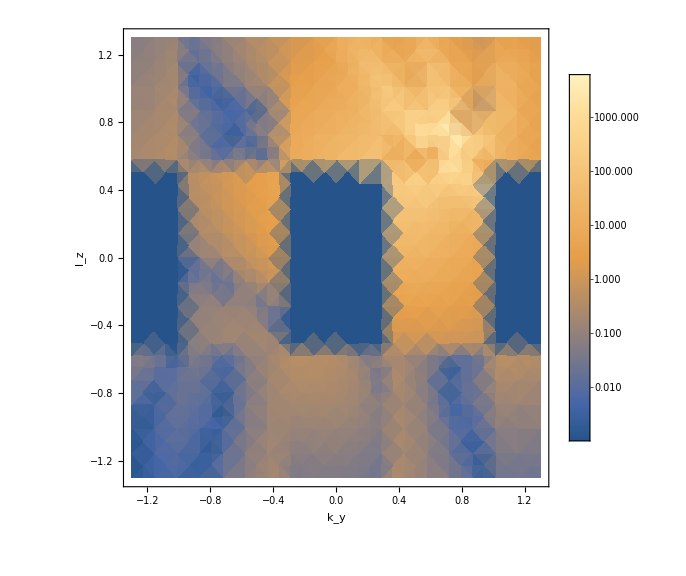

```mathematica
KLScanDensityPlotSumImYZColoured=Block[
{},
DensityPlot[Min[Max[Abs[Im[
EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,ky+kyRegulationThisSection,lz,cutID->CutIDLxB,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]+
EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,ky+kyRegulationThisSection,lz,cutID->CutIDBxL,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]]
],1.0*^-3],10*^5],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotLegends->Automatic,ScalingFunctions->"Log",
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->MaxRecursionForThisSection,
Frame->True,
ImageSize->ImageSizeForThisSection,PerformanceGoal->PerformanceGoalForThisSection]
]
```

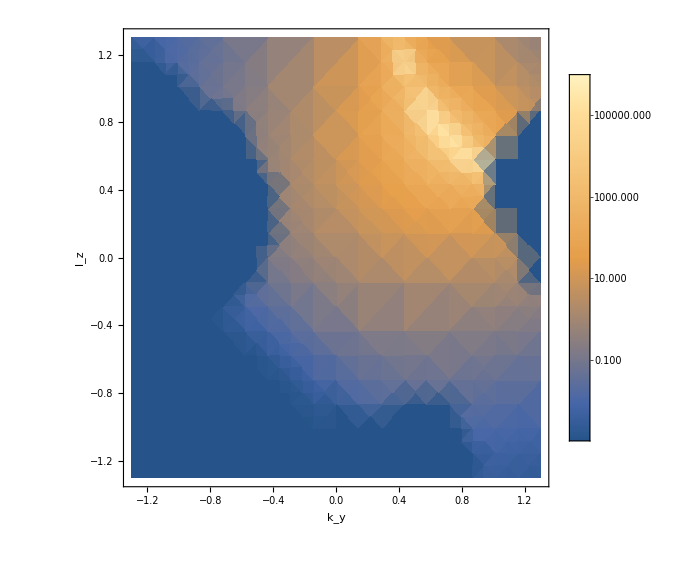

```mathematica
KLScanDensityPlotRealYZColoured=Block[
{},
DensityPlot[Min[Max[Abs[Re[2EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,ky+kyRegulationThisSection,lz,cutID->CutIDRA,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]]],1.0*^-3],10*^5],
{ky,-1.3,1.3},
{lz,-1.3,1.3},
PlotLegends->Automatic,ScalingFunctions->"Log", 
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->MaxRecursionForThisSection,
Frame->True,
ImageSize->ImageSizeForThisSection,PerformanceGoal->PerformanceGoalForThisSection]
]
```

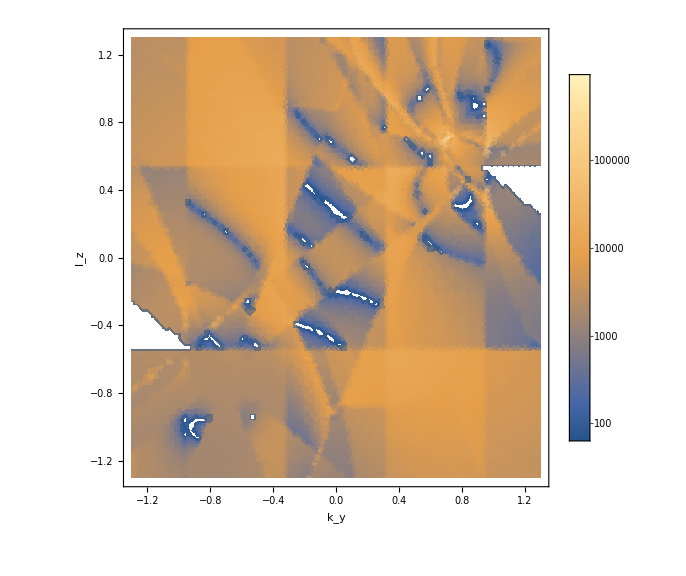

```mathematica
KLScanDensityPlotAllYZColouredWithMC=Block[
{},
DensityPlot[Min[Max[Abs[Re[
EvaluateFullForKLScanYZ[HookSemiInclusiveMCDeformation,ky+kyRegulationThisSection,lz,DEBUG->False,IncludeJacobian->True]
]],1.0*^-3],10*^5],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotLegends->Automatic,ScalingFunctions->"Log",
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->MaxRecursionForThisSection,
Frame->True,
ImageSize->ImageSizeForThisSection,PerformanceGoal->PerformanceGoalForThisSection]
]
```

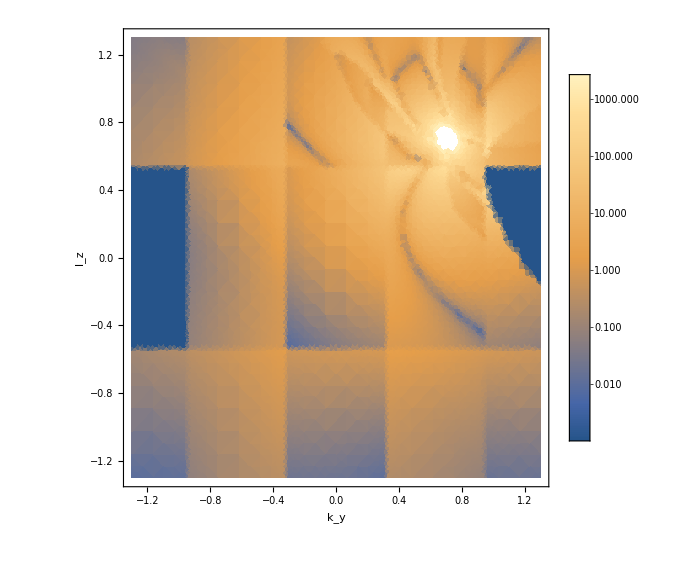

```mathematica
KLScanDensityPlotAllYZColoured=Block[
{},
DensityPlot[Min[Max[Abs[Re[
2EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,ky+kyRegulationThisSection,lz,cutID->CutIDRA,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]+
EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,ky+kyRegulationThisSection,lz,cutID->CutIDLxB,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]+
EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,ky+kyRegulationThisSection,lz,cutID->CutIDBxL,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]
]],1.0*^-3],10*^5],
{ky,-1.3,1.3},
{lz,-1.3,1.3}, 
PlotLegends->Automatic,ScalingFunctions->"Log",
PlotPoints->DensityForThisSection,Axes->True,AxesLabel->{"k_y","l_z"},MaxRecursion->MaxRecursionForThisSection,
Frame->True,
ImageSize->ImageSizeForThisSection,PerformanceGoal->PerformanceGoalForThisSection]
]
```

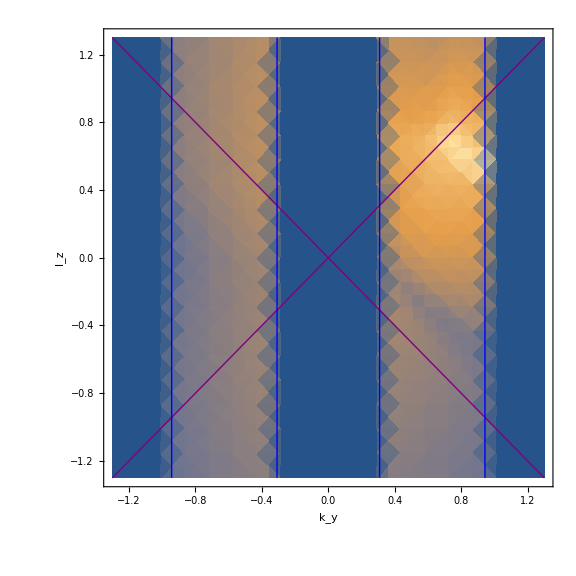
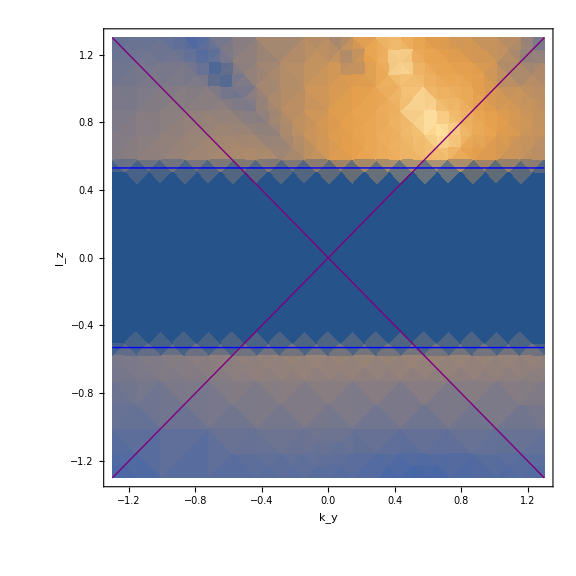
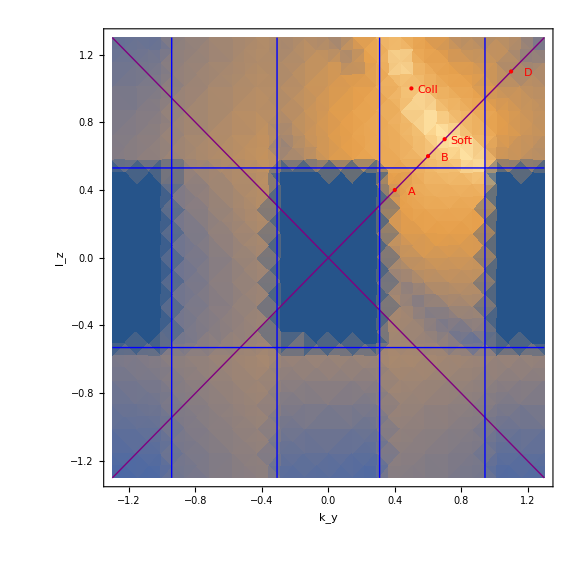
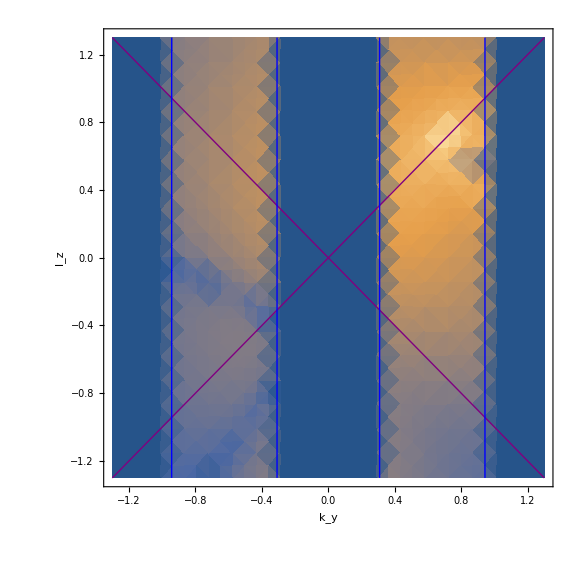
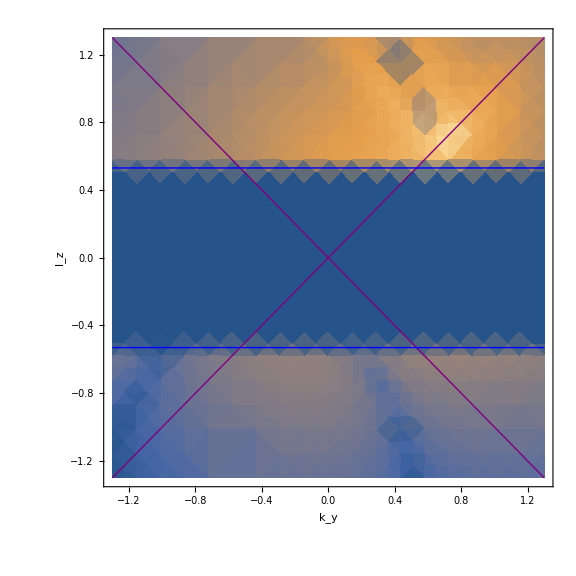
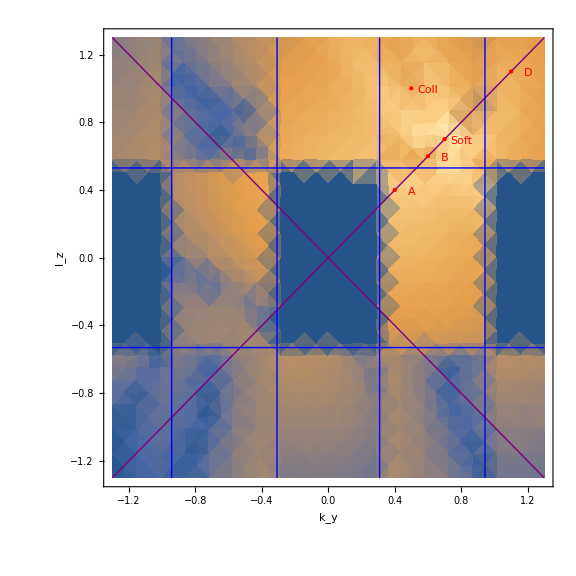
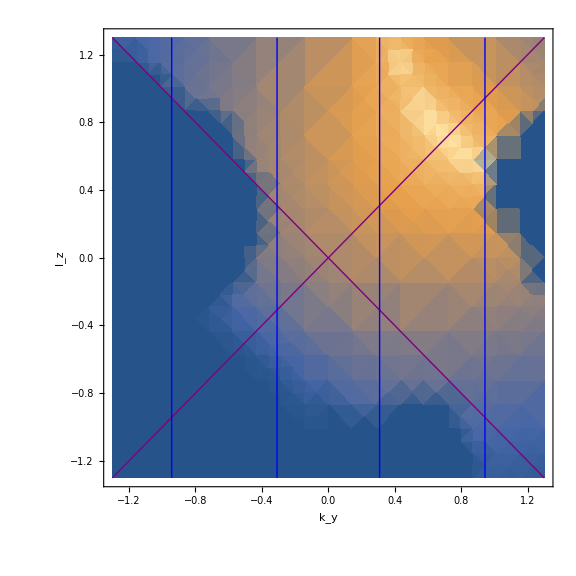
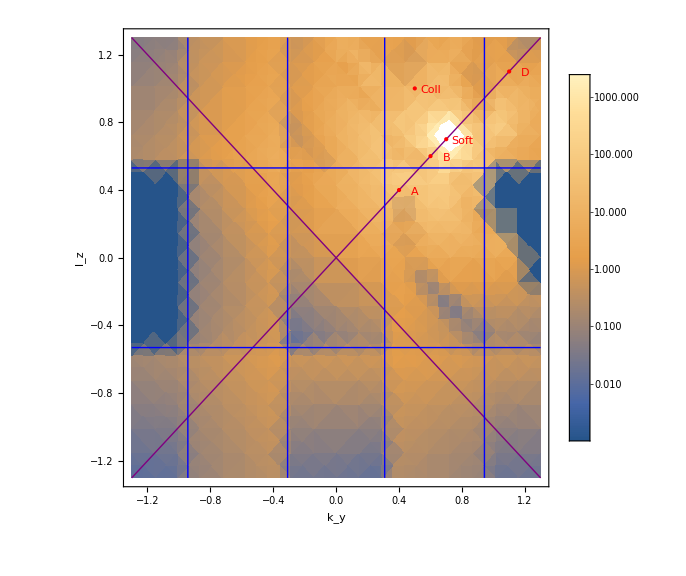
-Graphics-Re[LxB( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )] | -Graphics-Re[BxL( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )] | -Graphics-Re[(LxB+BxL)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]
-Graphics-Im[LxB( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )] | -Graphics-Im[BxL( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )] | -Graphics-Im[(LxB+BxL)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]
-Graphics-Real( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) ) | -Graphics-Re[(LxB+BxL+Real)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )] |

```mathematica
Grid[{
{
Labeled[Show[KLScanDensityPlotLxBReYZColoured⟦1⟧,AllThresholdLinesForKLScanInLxBYZ,ImageSize->Large],"Re[LxB( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"],
Labeled[Show[KLScanDensityPlotBxLReYZColoured⟦1⟧,AllThresholdLinesForKLScanInBxLYZ,ImageSize->Large],"Re[BxL( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"],
Labeled[Show[{KLScanDensityPlotSumReYZColoured⟦1⟧,AllThresholdLinesForKLScanInSumYZ,
Sequence[MakeALabeledPoint[{0.4,0.4},"A"]],
Sequence[MakeALabeledPoint[{0.6,0.6},"B"]],
Sequence[MakeALabeledPoint[{0.7,0.7},"Soft"]],
Sequence[MakeALabeledPoint[{1.1,1.1},"D"]],
Sequence[MakeALabeledPoint[{0.5,1.0},"Coll"]]
},ImageSize->Large],"Re[(LxB+BxL)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"]
},
{
Labeled[Show[KLScanDensityPlotLxBImYZColoured⟦1⟧,AllThresholdLinesForKLScanInLxBYZ,ImageSize->Large],"Im[LxB( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"],
Labeled[Show[KLScanDensityPlotBxLImYZColoured⟦1⟧,AllThresholdLinesForKLScanInBxLYZ,ImageSize->Large],"Im[BxL( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"],
Labeled[Show[{KLScanDensityPlotSumImYZColoured⟦1⟧,AllThresholdLinesForKLScanInSumYZ,
Sequence[MakeALabeledPoint[{0.4,0.4},"A"]],
Sequence[MakeALabeledPoint[{0.6,0.6},"B"]],
Sequence[MakeALabeledPoint[{0.7,0.7},"Soft"]],
Sequence[MakeALabeledPoint[{1.1,1.1},"D"]],
Sequence[MakeALabeledPoint[{0.5,1.0},"Coll"]]
},ImageSize->Large],"Im[(LxB+BxL)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"]
},
{
Labeled[Show[KLScanDensityPlotRealYZColoured⟦1⟧,AllThresholdLinesForKLScanInLxBYZ,ImageSize->Large],"Real( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )"],
Labeled[Show[{KLScanDensityPlotAllYZColoured,AllThresholdLinesForKLScanInSumYZ,
Sequence[MakeALabeledPoint[{0.4,0.4},"A"]],
Sequence[MakeALabeledPoint[{0.6,0.6},"B"]],
Sequence[MakeALabeledPoint[{0.7,0.7},"Soft"]],
Sequence[MakeALabeledPoint[{1.1,1.1},"D"]],
Sequence[MakeALabeledPoint[{0.5,1.0},"Coll"]]
},ImageSize->Large],"Re[(LxB+BxL+Real)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )]"]
}

},ItemSize->{55,35}]
```

### Phase map, with deformation

And now the same but with actual a full colour scale on the density plot

```mathematica
RefreshHooks[];
```

```mathematica
DensityForThisSection=Automatic;
MaxRecursionForThisSection=Automatic;
PerformanceGoalForThisSection="Quality";
IncludeJacobianInThisSection=False;
ImageSizeForThisSection=Large;
PlotThemeForThisSection="Default";
ColorFunctionForThisSection="CyclicLogAbs"(*"CyclicLogAbsArg"*);
RegulatorForThisSection=10^-10;
kyRegulationThisSection=10^-5;
```

```mathematica
HookForThisSection=HookSemiInclusiveNoMCDeformation;
```

```mathematica
KLScanDensityPlotLxBYZColoured=Block[
{},
ComplexPlot[
EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,Re[z]+kyRegulationThisSection,Im[z],cutID->CutIDLxB,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]+RegulatorForThisSection
,{z,-1.3-1.3 I,+1.3+1.3 I},
PlotLegends->Automatic,Axes->True,AxesLabel->{"k_y","l_z"},ColorFunction->ColorFunctionForThisSection,
PlotPoints->DensityForThisSection,MaxRecursion->MaxRecursionForThisSection,
ImageSize->ImageSizeForThisSection,PerformanceGoal->PerformanceGoalForThisSection,Frame->True,PlotTheme->PlotThemeForThisSection]
]
```

$Aborted

```mathematica
KLScanDensityPlotBxLYZColoured=Block[
{},
ComplexPlot[
EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,Re[z]+kyRegulationThisSection,Im[z],cutID->CutIDBxL,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]+RegulatorForThisSection
,{z,-1.3-1.3 I,+1.3+1.3 I},
PlotLegends->Automatic,Axes->True,AxesLabel->{"k_y","l_z"},ColorFunction->ColorFunctionForThisSection,
PlotPoints->DensityForThisSection,MaxRecursion->MaxRecursionForThisSection,
ImageSize->ImageSizeForThisSection,PerformanceGoal->PerformanceGoalForThisSection,Frame->True,PlotTheme->PlotThemeForThisSection]
]
```

```mathematica
KLScanDensityPlotSumYZColoured=Block[
{},
ComplexPlot[
EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,Re[z]+kyRegulationThisSection,Im[z],cutID->CutIDLxB,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]+
EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,Re[z]+kyRegulationThisSection,Im[z],cutID->CutIDBxL,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]+RegulatorForThisSection
,{z,-1.3-1.3 I,+1.3+1.3 I},
PlotLegends->Automatic,Axes->True,AxesLabel->{"k_y","l_z"},ColorFunction->ColorFunctionForThisSection,
PlotPoints->DensityForThisSection,MaxRecursion->MaxRecursionForThisSection,
ImageSize->ImageSizeForThisSection,PerformanceGoal->PerformanceGoalForThisSection,Frame->True,PlotTheme->PlotThemeForThisSection]
]
```

```mathematica
KLScanDensityPlotRYZColoured=Block[
{},
ComplexPlot[
Abs[2 Re[EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,Re[z]+kyRegulationThisSection,Im[z],cutID->CutIDRA,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]]]-RegulatorForThisSection-10^-3 RegulatorForThisSection ⅈ
,{z,-1.3-1.3 I,+1.3+1.3 I},
PlotLegends->Automatic,Axes->True,AxesLabel->{"k_y","l_z"},ColorFunction->"CyclicLogAbs",
PlotPoints->DensityForThisSection,MaxRecursion->MaxRecursionForThisSection,
ImageSize->ImageSizeForThisSection,PerformanceGoal->PerformanceGoalForThisSection,Frame->True,PlotTheme->PlotThemeForThisSection]
]
```

```mathematica
KLScanDensityPlotAllYZColoured=Block[
{},
ComplexPlot[
2 EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,Re[z]+kyRegulationThisSection,Im[z],cutID->CutIDRA,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]+
EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,Re[z]+kyRegulationThisSection,Im[z],cutID->CutIDLxB,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]+
EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,Re[z]+kyRegulationThisSection,Im[z],cutID->CutIDBxL,DEBUG->False,IncludeJacobian->IncludeJacobianInThisSection]+RegulatorForThisSection
,{z,-1.3-1.3 I,+1.3+1.3 I},
PlotLegends->Automatic,Axes->True,AxesLabel->{"k_y","l_z"},ColorFunction->ColorFunctionForThisSection,
PlotPoints->DensityForThisSection,MaxRecursion->MaxRecursionForThisSection,
ImageSize->ImageSizeForThisSection,PerformanceGoal->PerformanceGoalForThisSection,Frame->True,PlotTheme->PlotThemeForThisSection]
]
```

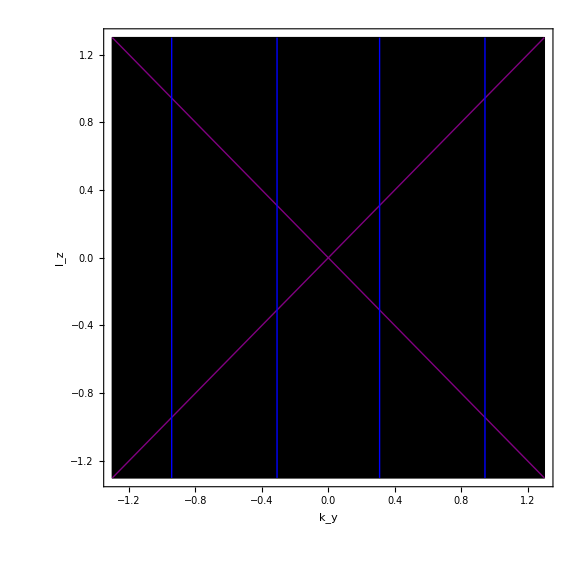
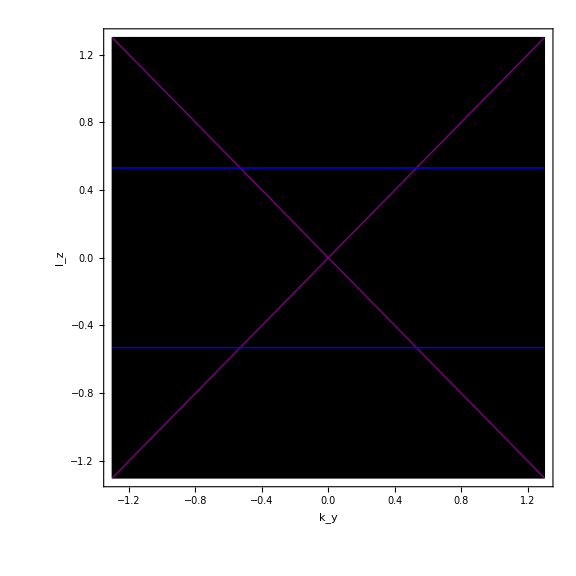
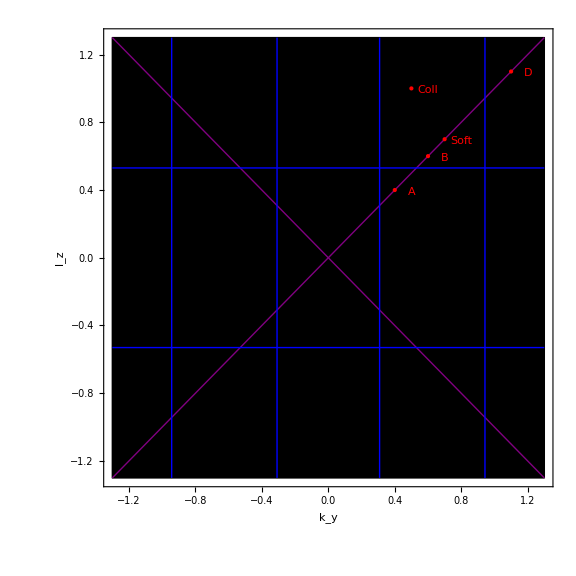
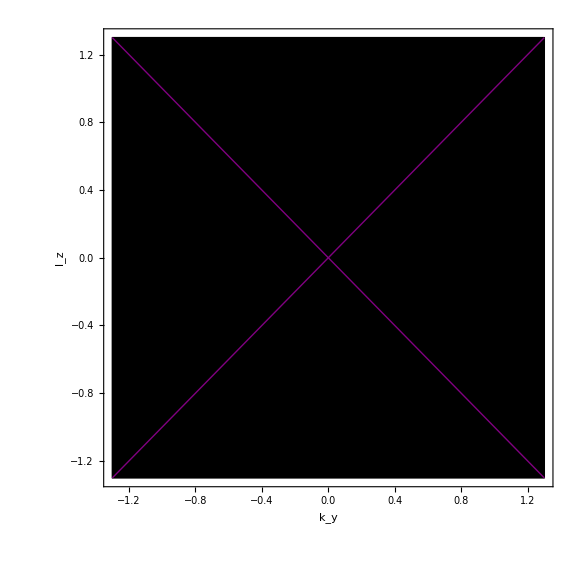
-Graphics-LxB( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) ) | -Graphics-BxL( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) ) | -Graphics-(LxB+BxL)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )
-Graphics-BxL( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) ) | -Graphics-(LxB+BxL+Real)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) ) |

```mathematica
Grid[{
{
Labeled[Show[KLScanDensityPlotLxBYZColoured⟦1⟧,AllThresholdLinesForKLScanInLxBYZ,ImageSize->Large],"LxB( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )"],
Labeled[Show[KLScanDensityPlotBxLYZColoured⟦1⟧,AllThresholdLinesForKLScanInBxLYZ,ImageSize->Large],"BxL( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )"],
Labeled[Show[{KLScanDensityPlotSumYZColoured⟦1⟧,AllThresholdLinesForKLScanInSumYZ,
Sequence[MakeALabeledPoint[{0.4,0.4},"A"]],
Sequence[MakeALabeledPoint[{0.6,0.6},"B"]],
Sequence[MakeALabeledPoint[{0.7,0.7},"Soft"]],
Sequence[MakeALabeledPoint[{1.1,1.1},"D"]],
Sequence[MakeALabeledPoint[{0.5,1.0},"Coll"]]
},ImageSize->Large],"(LxB+BxL)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )"]
},
{
Labeled[Show[KLScanDensityPlotRYZColoured⟦1⟧,
Graphics[
{
{Purple,Thick,Line[{{-1.3,-1.3},{1.3,1.3}}]},
{Purple,Thick,Line[{{-1.3,1.3},{1.3,-1.3}}]}
}]
,ImageSize->Large],"(RA+RB)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )"],
Labeled[Show[{KLScanDensityPlotAllYZColoured,AllThresholdLinesForKLScanInSumYZ,
Sequence[MakeALabeledPoint[{0.4,0.4},"A"]],
Sequence[MakeALabeledPoint[{0.6,0.6},"B"]],
Sequence[MakeALabeledPoint[{0.7,0.7},"Soft"]],
Sequence[MakeALabeledPoint[{1.1,1.1},"D"]],
Sequence[MakeALabeledPoint[{0.5,1.0},"Coll"]]
},ImageSize->Large],"(LxB+BxL+RA+RB)( ( 0, k_y , 1/(√2)), (0 , 1/(√2) , l_z) )"]
}

},ItemSize->{55,35}]
```

### ComplexPlot3D

```mathematica
RegulatorForThisSection=10^-10;
```

```mathematica
GlobalCount=0;
GlobalIndicator=PrintTemporary["Starting hooks..."];
LastIndication=Now;
LastRefresh=Now;
LastCallArgs=Null;
LastRes=Null;
NIdentical=0;
RefreshHooks[];
startTime=Now;
MyFunc[z_?NumericQ]:=Block[{TMP,Res},
GlobalCount+=1;
If[QuantityMagnitude[UnitConvert[Now-LastRefresh,"s"]]>3600,
LastRefresh=Now;
GlobalIndicator=PrintTemporary[DateString[]<>" : Now refreshing hooks... (current function evaluation count: "<>ToString[GlobalCount,InputForm]<>" )"];
RefreshHooks[];
Pause[0.5];
];
If[QuantityMagnitude[UnitConvert[Now-LastIndication,"s"]]>5,
NotebookDelete[GlobalIndicator];GlobalIndicator=PrintTemporary[DateString[]<>" : Current function evaluation count: "<>ToString[GlobalCount,InputForm]<>" ( "<>
ToString[Round[(GlobalCount-NIdentical)/(QuantityMagnitude[UnitConvert[Now-startTime,"s"]])]]
<>" evals/s)"<>", #Recycles: "<>ToString[NIdentical]];
LastIndication=Now;
];
(*MyPrint["Last args received: "<>ToString[LastCallArgs,InputForm]<>", Args received: "<>ToString[{N[Re[z],16],N[Im[z],16]},InputForm]<>"N Identical: "<>ToString[NIdentical]<>" Test:"<>ToString[TrueQ[{N[Re[z],16],N[Im[z],16]}==LastCallArgs]]];Pause[1.0];*)
If[TrueQ[{N[Re[z],16],N[Im[z],16]}==LastCallArgs],
NIdentical+=1;
,
LastCallArgs={N[Re[z],16],N[Im[z],16]};
Res=EvaluateFullForKLScanYZ[HookSemiInclusiveNoMCDeformation,Re[z],Im[z],DEBUG->False,IncludeJacobian->False]+RegulatorForThisSection;
(*Res=2EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,Re[z],Im[z],cutID->CutIDRA,DEBUG->False]+
EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,Re[z],Im[z],cutID->CutIDLxB,DEBUG->False]+
EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,Re[z],Im[z],cutID->CutIDBxL,DEBUG->False]*)
LastRes=Res;
];
LastRes
]
kyLowBound=0.5;kyUpBound=0.9;lzLowBound=0.5;lzUpBound=0.9;
(*kyLowBound=-1.3;kyUpBound=1.3;lzLowBound=-1.3;lzUpBound=1.3;*)
ComplexPlot3D[
MyFunc[z]
,{z,kyLowBound+lzLowBound I,kyUpBound+lzUpBound I},
PlotLegends->Automatic,Axes->True,AxesLabel->{"k_y","l_z"},ColorFunction->"CyclicLogAbs",
ImageSize->Large,PerformanceGoal->"Quality",ScalingFunctions->"Log",PlotTheme->"Default"
(*,MaxRecursion->3,PlotPoints->2*)]
```

-Graphics3D-

```mathematica
GlobalCount=0;
GlobalIndicator=PrintTemporary["Starting hooks..."];
LastIndication=Now;
LastRefresh=Now;
LastCallArgs=Null;
LastRes=Null;
NIdentical=0;
RefreshHooks[];
startTime=Now;
MyFunc[z_?NumericQ]:=Block[{TMP,Res},
GlobalCount+=1;
If[QuantityMagnitude[UnitConvert[Now-LastRefresh,"s"]]>3600,
LastRefresh=Now;
GlobalIndicator=PrintTemporary[DateString[]<>" : Now refreshing hooks... (current function evaluation count: "<>ToString[GlobalCount,InputForm]<>" )"];
RefreshHooks[];
Pause[0.5];
];
If[QuantityMagnitude[UnitConvert[Now-LastIndication,"s"]]>5,
NotebookDelete[GlobalIndicator];GlobalIndicator=PrintTemporary[DateString[]<>" : Current function evaluation count: "<>ToString[GlobalCount,InputForm]<>" ( "<>
ToString[Round[(GlobalCount-NIdentical)/(QuantityMagnitude[UnitConvert[Now-startTime,"s"]])]]
<>" evals/s)"<>", #Recycles: "<>ToString[NIdentical]];
LastIndication=Now;
];
(*MyPrint["Last args received: "<>ToString[LastCallArgs,InputForm]<>", Args received: "<>ToString[{N[Re[z],16],N[Im[z],16]},InputForm]<>"N Identical: "<>ToString[NIdentical]<>" Test:"<>ToString[TrueQ[{N[Re[z],16],N[Im[z],16]}==LastCallArgs]]];Pause[1.0];*)
If[TrueQ[{N[Re[z],16],N[Im[z],16]}==LastCallArgs],
NIdentical+=1;
,
LastCallArgs={N[Re[z],16],N[Im[z],16]};
Res=EvaluateFullForKLScanYZ[HookSemiInclusiveNoMCDeformation,Re[z],Im[z],DEBUG->False,IncludeJacobian->False]+RegulatorForThisSection;
(*Res=2EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,Re[z],Im[z],cutID->CutIDRA,DEBUG->False]+
EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,Re[z],Im[z],cutID->CutIDLxB,DEBUG->False]+
EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,Re[z],Im[z],cutID->CutIDBxL,DEBUG->False]*)
LastRes=Res;
];
LastRes
]
(*kyLowBound=0.5;kyUpBound=0.9;lzLowBound=0.5;lzUpBound=0.9;*)
kyLowBound=-1.3;kyUpBound=1.3;lzLowBound=-1.3;lzUpBound=1.3;
ComplexPlot3D[
MyFunc[z]
,{z,kyLowBound+lzLowBound I,kyUpBound+lzUpBound I},
PlotLegends->Automatic,Axes->True,AxesLabel->{"k_y","l_z"},ColorFunction->"CyclicLogAbs",
ImageSize->Large,PerformanceGoal->"Quality",ScalingFunctions->"Log",PlotTheme->"Default"
(*,MaxRecursion->3,PlotPoints->2*)]
```

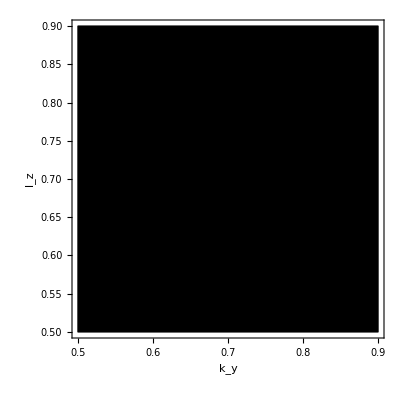

```mathematica
GlobalCount=0;
GlobalIndicator=PrintTemporary["Starting hooks..."];
LastIndication=Now;
LastRefresh=Now;
LastCallArgs=Null;
LastRes=Null;
NIdentical=0;
RefreshHooks[];
startTime=Now;
MyFunc[z_?NumericQ]:=Block[{TMP,Res},
GlobalCount+=1;
If[QuantityMagnitude[UnitConvert[Now-LastRefresh,"s"]]>3600,
LastRefresh=Now;
GlobalIndicator=PrintTemporary[DateString[]<>" : Now refreshing hooks... (current function evaluation count: "<>ToString[GlobalCount,InputForm]<>" )"];
RefreshHooks[];
Pause[0.5];
];
If[QuantityMagnitude[UnitConvert[Now-LastIndication,"s"]]>5,
NotebookDelete[GlobalIndicator];GlobalIndicator=PrintTemporary[DateString[]<>" : Current function evaluation count: "<>ToString[GlobalCount,InputForm]<>" ( "<>
ToString[Round[(GlobalCount-NIdentical)/(QuantityMagnitude[UnitConvert[Now-startTime,"s"]])]]
<>" evals/s)"<>", #Recycles: "<>ToString[NIdentical]];
LastIndication=Now;
];
(*MyPrint["Last args received: "<>ToString[LastCallArgs,InputForm]<>", Args received: "<>ToString[{N[Re[z],16],N[Im[z],16]},InputForm]<>"N Identical: "<>ToString[NIdentical]<>" Test:"<>ToString[TrueQ[{N[Re[z],16],N[Im[z],16]}==LastCallArgs]]];Pause[1.0];*)
If[TrueQ[{N[Re[z],16],N[Im[z],16]}==LastCallArgs],
NIdentical+=1;
,
LastCallArgs={N[Re[z],16],N[Im[z],16]};
Res=EvaluateFullForKLScanYZ[HookSemiInclusiveNoMCDeformation,Re[z],Im[z],DEBUG->False,IncludeJacobian->False]+RegulatorForThisSection;
(*Res=2EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,Re[z],Im[z],cutID->CutIDRA,DEBUG->False]+
EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,Re[z],Im[z],cutID->CutIDLxB,DEBUG->False]+
EvaluateCutForKLScanYZ[HookSemiInclusiveNoMCDeformation,Re[z],Im[z],cutID->CutIDBxL,DEBUG->False]*)
LastRes=Res;
];
LastRes
]
kyLowBound=0.5;kyUpBound=0.9;lzLowBound=0.5;lzUpBound=0.9;
(*kyLowBound=-1.3;kyUpBound=1.3;lzLowBound=-1.3;lzUpBound=1.3;*)
ComplexPlot[
MyFunc[z]
,{z,kyLowBound+lzLowBound I,kyUpBound+lzUpBound I},
PlotLegends->Automatic,Axes->True,AxesLabel->{"k_y","l_z"},ColorFunction->"CyclicLogAbs",
ImageSize->Large,PerformanceGoal->"Quality",PlotTheme->"Default",
MaxRecursion->Automatic,PlotPoints->20]
```

### Results and experiments

ComplexPlot function around soft

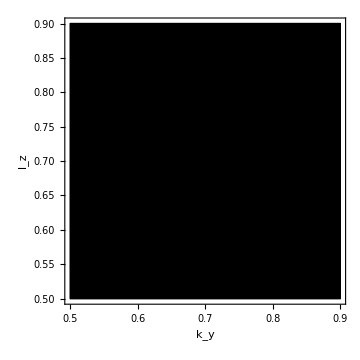

Soft Volcano zoom-in no color shading

-Graphics3D-

Soft Volcano zoom-in

-Graphics3D-

```mathematica
ComplexPlot3D[
EvaluateFullForKLScanYZ[HookSemiInclusiveNoMCDeformation,Re[z],Im[z],DEBUG->False,IncludeJacobian->False]
,{z,-1.3-1.3I,1.3+1.3I},
PlotLegends->Automatic,Axes->True,AxesLabel->{"k_y","l_z"},ColorFunction->"CyclicLogAbsArg",
ImageSize->Large,PerformanceGoal->"Quality",ScalingFunctions->"Log"
(*,MaxRecursion->3,PlotPoints->2*)]
```

$Aborted

```mathematica
GlobalCount
```

35127

```mathematica
EvaluateFullForKLScanYZ[HookSemiInclusiveNoMCDeformation,0.5,0.1,DEBUG->False,IncludeJacobian->False]
```

-4.89326-31.6213 ⅈ

```mathematica
RefreshHooks[];
```

```mathematica
AbsoluteTiming[For[ii=1,ii<=1000,ii++,
ExternalEvaluate[
HookSemiInclusiveNoMCDeformation,<|"Command"->"API_evaluate_integrand","Arguments"->{False,{RandomReal[],RandomReal[],RandomReal[],RandomReal[],RandomReal[],RandomReal[]}}|>]
]]
```

{1.30157,Null}

```mathematica
AbsoluteTiming[For[ii=1,ii<=1000,ii++,
RFM$EvaluateIntegrand[HookSemiInclusiveNoMCDeformation,{RandomReal[],RandomReal[],RandomReal[],RandomReal[],RandomReal[],RandomReal[]}]
]]
```

{0.641885,Null}

```mathematica
GlobalCount=0;
GlobalIndicator=Null;
MyFuncTest[z_?NumericQ]:=Block[{},
GlobalCount+=1;
If[Mod[GlobalCount,10000]==0,
If[Not[TrueQ[GlobalIndicator==Null]],
NotebookDelete[GlobalIndicator];
];
GlobalIndicator=PrintTemporary["Current function evaluation count: "<>ToString[GlobalCount,InputForm]];
];
((Re[z]+ⅈ Im[z])^2+1)/((Re[z]+ⅈ Im[z])^2-1)
]
ComplexPlot3D[MyFuncTest[z],{z,-2-2I,2+2I},
PlotLegends->Automatic,PlotRange->Full,Axes->True,AxesLabel->{"k_y","l_z"},ColorFunction->"CyclicLogAbs",ImageSize->Large,PerformanceGoal->"Quality",ScalingFunctions->"Log"]
GlobalCount
```

-Graphics3D-

257864